```mathematica
basis={{1,0},{-0.5,Sqrt[3]/2}};
```

```mathematica
latticePoints=Flatten[Table[(i*basis[[1]]+j*basis[[2]]),{i,-5,5},{j,-5,5}],1];
```

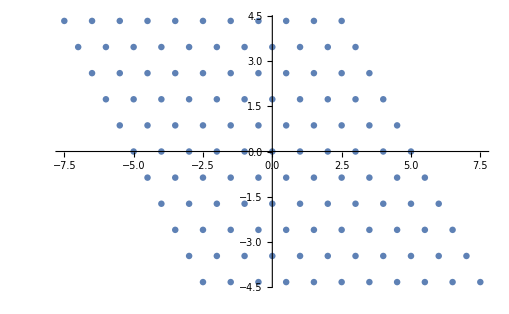

```mathematica
ListPlot[latticePoints]
```

```mathematica
triangularCell[a_Integer,b_Integer]:=a*basis[[1]]+b*basis[[2]];
triangularCell[1,1]
```

{1.5,-(√3)/2}

```mathematica
triangularCellCenter[a_Integer,b_Integer]:=(a+0.5)basis[[1]]+(b+0.5)
```

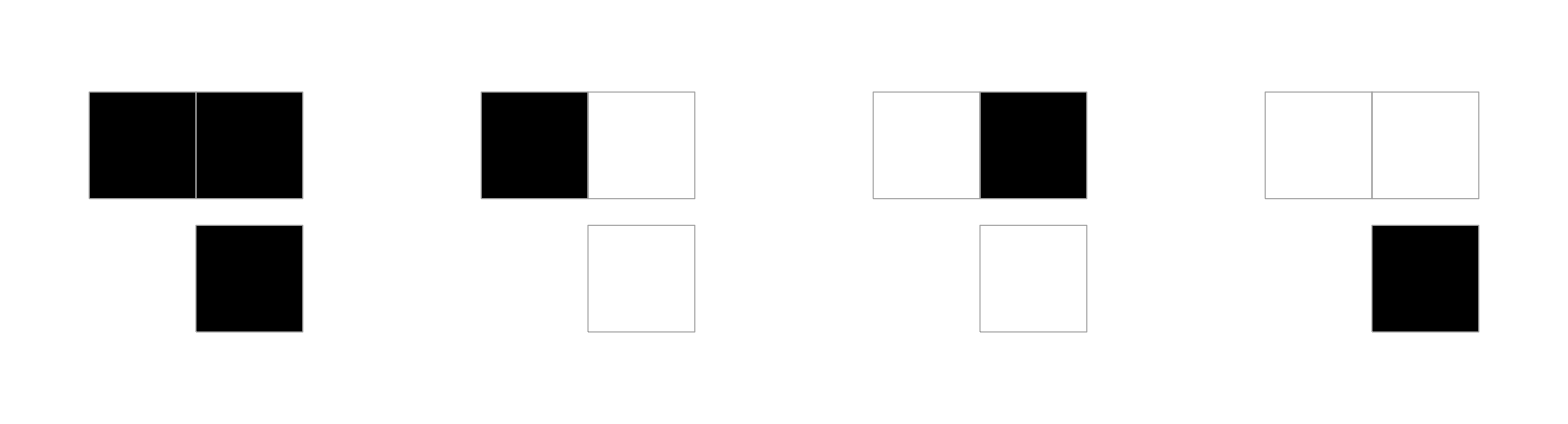

```mathematica
Cell[BoxData[
 RowBox[{"RulePlot", "[", 
  RowBox[{
   RowBox[{"CellularAutomaton", "[", 
    RowBox[{"{", 
     RowBox[{"9", ",", "2", ",", 
      RowBox[{"1", "/", "2"}]}], "}"}], "]"}], ",", 
   RowBox[{"Appearance", "\[Rule]", "\"\<Squares\>\""}]}], "]"}]], "Input",
 CellChangeTimes->{{3.77099560654987*^9, 3.770995608045824*^9}, {3.7709985690840673`*^9, 3.7709985744935985`*^9}},
 CellLabel->"In[71]:="]
```

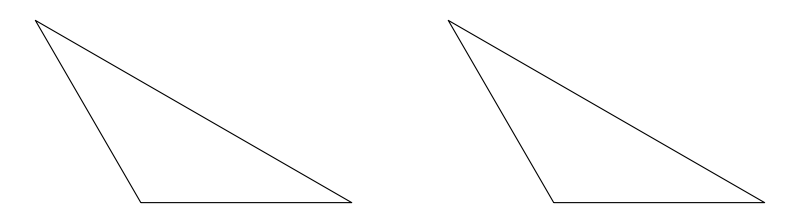

```mathematica
basisTriangle[basis,t_Integer]:=Graphics[{EdgeForm[Black],FaceForm[White],Triangle[{{0,0},basis[[1]],basis[[2]]}]}];
normal=GraphicsRow[{basisTriangle[basis,1],basisTriangle[basis,1]}]
```

```mathematica
inverted=Rotate[GraphicsRow[{basisTriangle[basis,1],basisTriangle[basis,1]}],Pi]
```

-Graphics-

```mathematica
Show[normal,inverted]
```

Show::gcomb: Could not combine the graphics objects in Show[,].